```mathematica
Simplify[-(1/(nb+1)*Log[1/(nb+1)^2] +nb/(nb+1)*Log[8/(nb+1)^2])]
```

-(Log[1/(1+nb)^2]+nb Log[8/(1+nb)^2])/(1+nb)

```mathematica
Simplify[-(2/(nb+2)*Log[2/(nb+2)/(nb+1)] + nb/(nb+2)*Log[6/(nb+1)/(nb+2)])]
```

-(2 Log[2/(2+3 nb+nb^2)]+nb Log[6/(2+3 nb+nb^2)])/(2+nb)

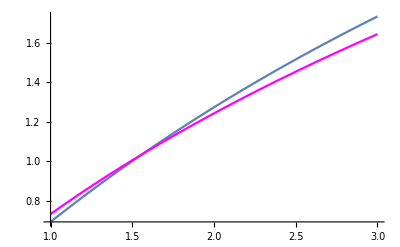

```mathematica
pti = Plot[-(1/(nb+1)*Log[1/(nb+1)^2] +nb/(nb+1)*Log[4/(nb+1)^2]), {nb, 1, 3}];
pt0 = Plot[-(2/(nb+2)*Log[2/(nb+2)/(nb+1)] + nb/(nb+2)*Log[6/(nb+1)/(nb+2)]), {nb, 1, 3}, PlotStyle->Magenta];
Show[pti, pt0]
```

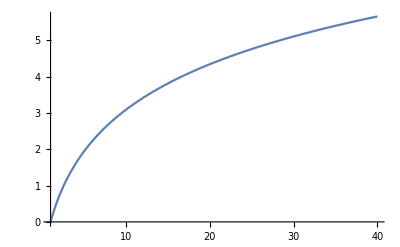

```mathematica
Plot[Log[((nb+1)*nb/2 + nb+1)/3], {nb, 1, 40}]
```

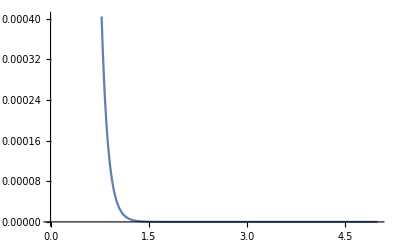

```mathematica
Plot[Exp[-10*x], {x, 0, 5}]
```

```mathematica
N[2*
π/5]
```

1.25664

```mathematica
N[2/3Log[3]]
```

0.732408

```mathematica
N[Log[2] +1/3Log[3]]
```

1.05935

```mathematica
N[Log[6] -2/3Log[3]]
```

1.05935

```mathematica
1/3Log[3]  +2/3Log[3/2]
```

2/3 Log[3/2]+Log[3]/3

```mathematica
N[%]
```

0.636514

```mathematica
L = 100000000;
l=L/2;
Ntot = 3;
n = 1;
a=1/100000π^2/2*(n/l^2+(Ntot-n)/(L-l)^2);
Integrate[Exp[-a*x^2], {x,1,100000000}] 
N[%]
```

-5000000000 √(5/(3 π)) (Erf[(√(3/5) π)/10000000000]-Erf[1/100 √(3/5) π])

9.99803×10^7

```mathematica
N[%]
```

1.35053

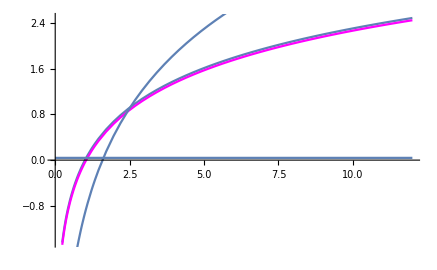

```mathematica
p1 = Plot[Log[x], {x, 0, 12}];
(*indistinguishable wrong!*)
p2 = Plot[Log[x*2] -2/3Log[3], {x, 0,12}, PlotStyle->Magenta];
p3 = Plot[Log[x] - Log[2*x] -2/3*Log[1/3], {x,0, 12}];
(*distinguishable*)
p4 = Plot[Log[x^2] + 2/3*Log[1/4],{x, 0, 12}];
Show[p1,p2, p3, p4]
```

```mathematica
Log[1/2]-2/3Log[1/3]
```

-Log[2]+(2 Log[3])/3

```mathematica
N[%]
```

0.039261

```mathematica
Simplify[Log[x] - Log[2*x]]
```

Log[x]-Log[2 x]

```mathematica
Plot[Log[x] - Log[2*x],{x, 0,10}]
```

-Graphics-

```mathematica
Log[1]-Log[2]
```

-Log[2]

```mathematica
N[%]
```

-0.693147

```mathematica
%-2/3*Log[1/3]
```

0.039261

## Wave Fkt and probs for Entropy in pos space

## Single infinite well

```mathematica
ClearAll[]
```

```mathematica
(*wave function*)
psi[x_, n_, L_] = Sin[x*n*π/L]
```

Sin[(n π x)/L]

```mathematica
psi1[x_] = psi[x]//.{n-> 1, L-> 10}
psi2[x_] = psi[x]//.{n-> 2, L-> 10}
```

Set::write: Tag Sin in Sin[(π x1)/10][x_] is Protected.

Sin[(π x)/10]

Set::write: Tag Sin in Sin[(π x2)/5][x_] is Protected.

Sin[(π x)/5]

```mathematica
(*TG limit*)
psiTG= Abs[psi1[x1]*psi2[x2] - psi1[x2]psi2[x1]]
```

Abs[-Sin[(π x1)/10][x2] Sin[(π x2)/5][x1]+Sin[(π x1)/10][x1] Sin[(π x2)/5][x2]]

```mathematica
Plot[Abs[psi1]^2, {x, 0, 10}]
Plot[Abs[psi2]^2, {x, 0, 10}]
DensityPlot[Abs[psiTG]^2, {x1,0,10},{x2,0, 10}]
```

-Graphics-

-Graphics-

-Graphics-

## quick S calc for n2

```mathematica
DoublePartWF = Abs[-HeavisideTheta[5-x1] ((-ⅇ^(-6.28318530717958647692528676655900576839`20. ⅈ-0.62831853071795864769252867665590057684`20. ⅈ x1)+ⅇ^(0.62831853071795864769252867665590057684`20. ⅈ x1)) HeavisideTheta[-x1]^2+((-1.`15.698970004336019+0``31.954344055520657 ⅈ) ⅇ^(-6.28318530717958647692528676655900576839`20. ⅈ-0.62831853071795864769252867665590057684`20. ⅈ x1)+(1.`15.698970004336019+0``31.954344055520657 ⅈ) ⅇ^(0.62831853071795864769252867665590057684`20. ⅈ x1)) HeavisideTheta[-x1] HeavisideTheta[x1]+((-1.`15.397940008672036+0``31.653314059856676 ⅈ) ⅇ^(-6.28318530717958647692528676655900576839`20. ⅈ-0.62831853071795864769252867665590057684`20. ⅈ x1)+(1.`15.397940008672036+0``31.653314059856676 ⅈ) ⅇ^(0.62831853071795864769252867665590057684`20. ⅈ x1)) HeavisideTheta[x1]^2) HeavisideTheta[5+x1] HeavisideTheta[5-x2] ((-ⅇ^(-6.28287116362398874631576032337391618939`20. ⅈ-0.62828711636239887463157603233739161894`20. ⅈ x2)+ⅇ^(0.62828711636239887463157603233739161894`20. ⅈ x2)) HeavisideTheta[-x2]^2+((-2.467154322800358444768049938031`8.091144627447326*^-8-0.00015707177521539652307075411185918194`15.397929151445629 ⅈ) ⅇ^(-6.28287116362398874631576032337391618939`20. ⅈ-0.62828711636239887463157603233739161894`20. ⅈ x2)+(2.467154322800358444768049938031`8.091144627447326*^-8-0.00015707177521539652307075411185918194`15.397929151445629 ⅈ) ⅇ^(0.62828711636239887463157603233739161894`20. ⅈ x2)) HeavisideTheta[-x2] HeavisideTheta[x2]+((0.99999995065691354399283110463900123937`15.397918294490259-0.00031414355043079304614150822371836389`15.397929151445629 ⅈ) ⅇ^(-6.28287116362398874631576032337391618939`20. ⅈ-0.62828711636239887463157603233739161894`20. ⅈ x2)-(0.99999995065691354399283110463900123937`15.397918294490259+0.00031414355043079304614150822371836389`15.397929151445629 ⅈ) ⅇ^(0.62828711636239887463157603233739161894`20. ⅈ x2)) HeavisideTheta[x2]^2) HeavisideTheta[5+x2]+HeavisideTheta[5-x1] ((-ⅇ^(-6.28287116362398874631576032337391618939`20. ⅈ-0.62828711636239887463157603233739161894`20. ⅈ x1)+ⅇ^(0.62828711636239887463157603233739161894`20. ⅈ x1)) HeavisideTheta[-x1]^2+((-2.467154322800358444768049938031`8.091144627447326*^-8-0.00015707177521539652307075411185918194`15.397929151445629 ⅈ) ⅇ^(-6.28287116362398874631576032337391618939`20. ⅈ-0.62828711636239887463157603233739161894`20. ⅈ x1)+(2.467154322800358444768049938031`8.091144627447326*^-8-0.00015707177521539652307075411185918194`15.397929151445629 ⅈ) ⅇ^(0.62828711636239887463157603233739161894`20. ⅈ x1)) HeavisideTheta[-x1] HeavisideTheta[x1]+((0.99999995065691354399283110463900123937`15.397918294490259-0.00031414355043079304614150822371836389`15.397929151445629 ⅈ) ⅇ^(-6.28287116362398874631576032337391618939`20. ⅈ-0.62828711636239887463157603233739161894`20. ⅈ x1)-(0.99999995065691354399283110463900123937`15.397918294490259+0.00031414355043079304614150822371836389`15.397929151445629 ⅈ) ⅇ^(0.62828711636239887463157603233739161894`20. ⅈ x1)) HeavisideTheta[x1]^2) HeavisideTheta[5+x1] HeavisideTheta[5-x2] ((-ⅇ^(-6.28318530717958647692528676655900576839`20. ⅈ-0.62831853071795864769252867665590057684`20. ⅈ x2)+ⅇ^(0.62831853071795864769252867665590057684`20. ⅈ x2)) HeavisideTheta[-x2]^2+((-1.`15.698970004336019+0``31.954344055520657 ⅈ) ⅇ^(-6.28318530717958647692528676655900576839`20. ⅈ-0.62831853071795864769252867665590057684`20. ⅈ x2)+(1.`15.698970004336019+0``31.954344055520657 ⅈ) ⅇ^(0.62831853071795864769252867665590057684`20. ⅈ x2)) HeavisideTheta[-x2] HeavisideTheta[x2]+((-1.`15.397940008672036+0``31.653314059856676 ⅈ) ⅇ^(-6.28318530717958647692528676655900576839`20. ⅈ-0.62831853071795864769252867665590057684`20. ⅈ x2)+(1.`15.397940008672036+0``31.653314059856676 ⅈ) ⅇ^(0.62831853071795864769252867665590057684`20. ⅈ x2)) HeavisideTheta[x2]^2) HeavisideTheta[5+x2]]
barrierPairs = {{-5,-1.666666666665},{-1.666666666665,1.666666666665},{1.666666666665,5}}
```

Abs[-HeavisideTheta[5-x1] ((-ⅇ^(-6.2831853071795864769 ⅈ-0.62831853071795864769 ⅈ x1)+ⅇ^(0.62831853071795864769 ⅈ x1)) HeavisideTheta[-x1]^2+((-1.+0. ⅈ) ⅇ^(-6.2831853071795864769 ⅈ-0.62831853071795864769 ⅈ x1)+(1.+0. ⅈ) ⅇ^(0.62831853071795864769 ⅈ x1)) HeavisideTheta[-x1] HeavisideTheta[x1]+((-1.+0. ⅈ) ⅇ^(-6.2831853071795864769 ⅈ-0.62831853071795864769 ⅈ x1)+(1.+0. ⅈ) ⅇ^(0.62831853071795864769 ⅈ x1)) HeavisideTheta[x1]^2) HeavisideTheta[5+x1] HeavisideTheta[5-x2] ((-ⅇ^(-6.2828711636239887463 ⅈ-0.62828711636239887463 ⅈ x2)+ⅇ^(0.62828711636239887463 ⅈ x2)) HeavisideTheta[-x2]^2+((-2.4671543×10^-8-0.000157071775215397 ⅈ) ⅇ^(-6.2828711636239887463 ⅈ-0.62828711636239887463 ⅈ x2)+(2.4671543×10^-8-0.000157071775215397 ⅈ) ⅇ^(0.62828711636239887463 ⅈ x2)) HeavisideTheta[-x2] HeavisideTheta[x2]+((0.999999950656914-0.000314143550430793 ⅈ) ⅇ^(-6.2828711636239887463 ⅈ-0.62828711636239887463 ⅈ x2)-(0.999999950656914+0.000314143550430793 ⅈ) ⅇ^(0.62828711636239887463 ⅈ x2)) HeavisideTheta[x2]^2) HeavisideTheta[5+x2]+HeavisideTheta[5-x1] ((-ⅇ^(-6.2828711636239887463 ⅈ-0.62828711636239887463 ⅈ x1)+ⅇ^(0.62828711636239887463 ⅈ x1)) HeavisideTheta[-x1]^2+((-2.4671543×10^-8-0.000157071775215397 ⅈ) ⅇ^(-6.2828711636239887463 ⅈ-0.62828711636239887463 ⅈ x1)+(2.4671543×10^-8-0.000157071775215397 ⅈ) ⅇ^(0.62828711636239887463 ⅈ x1)) HeavisideTheta[-x1] HeavisideTheta[x1]+((0.999999950656914-0.000314143550430793 ⅈ) ⅇ^(-6.2828711636239887463 ⅈ-0.62828711636239887463 ⅈ x1)-(0.999999950656914+0.000314143550430793 ⅈ) ⅇ^(0.62828711636239887463 ⅈ x1)) HeavisideTheta[x1]^2) HeavisideTheta[5+x1] HeavisideTheta[5-x2] ((-ⅇ^(-6.2831853071795864769 ⅈ-0.62831853071795864769 ⅈ x2)+ⅇ^(0.62831853071795864769 ⅈ x2)) HeavisideTheta[-x2]^2+((-1.+0. ⅈ) ⅇ^(-6.2831853071795864769 ⅈ-0.62831853071795864769 ⅈ x2)+(1.+0. ⅈ) ⅇ^(0.62831853071795864769 ⅈ x2)) HeavisideTheta[-x2] HeavisideTheta[x2]+((-1.+0. ⅈ) ⅇ^(-6.2831853071795864769 ⅈ-0.62831853071795864769 ⅈ x2)+(1.+0. ⅈ) ⅇ^(0.62831853071795864769 ⅈ x2)) HeavisideTheta[x2]^2) HeavisideTheta[5+x2]]

{{-5,-1.66667},{-1.66667,1.66667},{1.66667,5}}

```mathematica
DPWFNorm  = 800.039999998042
```

800.04

```mathematica
(*define and calculate probability*)
pij[i_, j_]:= NIntegrate[Abs[DoublePartWF]^2, Flatten[{x1,barrierPairs[[i]]}], Flatten[{x2,barrierPairs[[j]]}],  WorkingPrecision-> 10]/DPWFNorm
Print["defined"]
probSingle= NIntegrate[Abs[DoublePartWF]^2, Flatten[{x1,barrierPairs[[1]]}], Flatten[{x2,barrierPairs[[1]]}]]/DPWFNorm;
Print["probSingle"];
Print[probSingle];
```

defined

NIntegrate::precw: The precision of the argument function (Abs[-HeavisideTheta[5-x1] ((Times[«2»]+Power[«2»]) HeavisideTheta[«1»]^2+(Times[«2»]+Times[«2»]) HeavisideTheta[Times[«2»]] HeavisideTheta[x1]+(Times[«2»]+Times[«2»]) HeavisideTheta[«1»]^2) HeavisideTheta[5+x1] HeavisideTheta[5-x2] («1») HeavisideTheta[5+x2]+«1»]^2) is less than WorkingPrecision (MachinePrecision).

probSingle

1.30974×10^-10

```mathematica
getProbArray[ngap_]:=
(
Clear[l];
l = {};
For[i =1, i<=   ngap,i++,
Clear[subl];
subl = {};
For[j= 1, j<= ngap, j++,
(*syntax: If[condition, case true, case false]*)
Print[i, j];
prob = pij[i,j];
Print[prob];
AppendTo[subl, prob];
]
AppendTo[l, subl];
]

l;
)

ngap = Length[barrierPairs];
Print["gamma"]
Print[gamma]
Print["ngap"]
Print[ngap]
getProbArray[ngap];
probList = l;
```

gamma

gamma

ngap

3

11

1.30974×10^-10

12

0.0786478

13

0.323589

21

0.0786478

22

0.0382305

23

0.0786478

31

0.323589

32

0.0786478

33

1.30974×10^-10

```mathematica
Print["probList"];
Print[probList];

reliefplot= ReliefPlot[probList];
```

probList

{{1.30974×10^-10,0.0786478,0.323589},{0.0786478,0.0382305,0.0786478},{0.323589,0.0786478,1.30974×10^-10}}

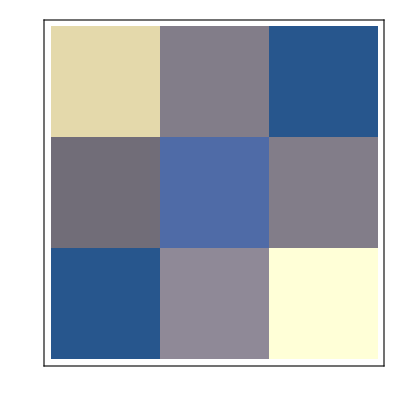

```mathematica
ReliefPlot[probList]
```

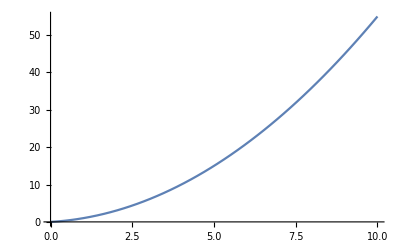

```mathematica
Plot[n*(n+1)/2, {n, 0, 10}]
```